# Masks Quiz

https://twitter.com/nntaleb/status/1270715896294633472

-Graphics-

-Graphics-
-Graphics-

It is the same as a single stylist seeing 140 people, assuming independence.

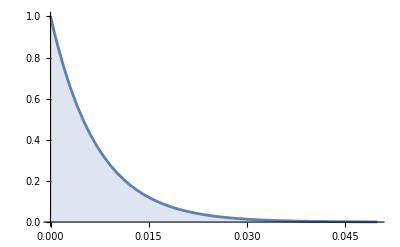

```mathematica
Plot[(1-p)^140,{p,0,0.05},PlotRange->All,Filling->Bottom]
```

```mathematica
TableForm[
Table[{p,(1-p)^140,CDF[BinomialDistribution[70,p],0]^2, CDF[BinomialDistribution[140,p],0]},{p,0.00,0.003,0.0005}],
TableHeadings->{None,{"p","(1-p)^140","Binomial"}}
]
```

p | (1-p)^140 | Binomial | 
0. | 1. | 1 | 1
0.0005 | 0.932377 | 0.932377 | 0.932377
0.001 | 0.869297 | 0.869297 | 0.869297
0.0015 | 0.810456 | 0.810456 | 0.810456
0.002 | 0.755572 | 0.755572 | 0.755572
0.0025 | 0.704379 | 0.704379 | 0.704379
0.003 | 0.656632 | 0.656632 | 0.656632

-Graphics-